# cooling laser TA installation

P. Huft.

```mathematica
SetDirectory[NotebookDirectory[]];
PGmmPerPixel=0.00375;(*for the Point Grey BFLY-PGE-12A2M-CS*)
λ780mm=7.8*^-4;
```

## 2023.06.16

Image of the cooling laser beam profile before the spectroscopy and AOMs branching to motivate which asphere I pick for launching the beam from the TA out of a single mode fiber.

```mathematica
data=ImageData[ColorConvert[Import["cooling_laser_after_first_PBS-2023-06-16-165749.bmp"],"Grayscale"]];
data =data[[300;;700,400;;800]];
data -=data[[-1,-1]];
data/=Max[data];
Image[data]
```

-Graphics-

```mathematica
{imax,jmax}=data//Dimensions;
dataCoordinated=Flatten[Table[{i,j,data[[i,j]]},{i,Range[imax]},{j,Range[jmax]}],1];
```

```mathematica
Clear[x0,y0,wx,wy];
model= Exp[(-2(x-x0)^2)/wx^2]Exp[(-2(y-y0)^2)/wy^2];
fit=FindFit[dataCoordinated,model,{{x0,216},{y0,230},{wx,70},{wy,70}},{x,y}]
{x0,y0,wx,wy}=Values[fit];
```

{x0→225.542,y0→209.785,wx→99.025,wy→102.05}

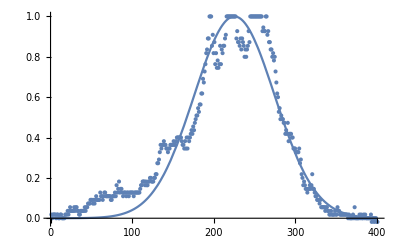

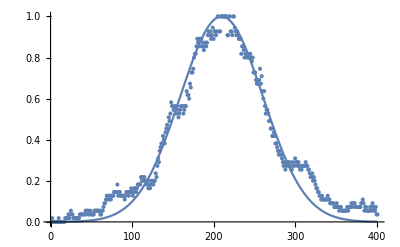

waist in x (mm)

0.371344

waist in y (mm)

0.382686

```mathematica
{xmax,ymax}=Dimensions[data];
Show[Plot[(model/.fit)/.y->y0,{x,0,xmax}],ListPlot[data[[;;,Floor[y0+0.5]]]],PlotRange->All]
Show[Plot[(model/.fit)/.x->x0,{y,0,ymax}],ListPlot[data[[Floor[x0+0.5],;;]]],PlotRange->All]
"waist in x (mm)"
wxmm=wx*PGmmPerPixel
"waist in y (mm)"
wymm=wy*PGmmPerPixel
```

```mathematica
(π*wxmm^2)/λ780mm
```

555.402

```mathematica
wxmm/wymm
```

0.970362

```mathematica
wavgmm=(wxmm+wymm)/2;
```

```mathematica
(wavgmm*2.5*^-3*π)/λ780mm
```

3.79624

```mathematica
4/%*wavgmm
```

0.397251

```mathematica
4.5/3.79
```

1.18734